# Practical 1

## Solution of first order differential equation

```mathematica
sol = DSolve[{y'[x] == y[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
A = y[x]/.sol/.{C[1] -> 1}
```

{ⅇ^x}

```mathematica
y[x]
```

y[x]

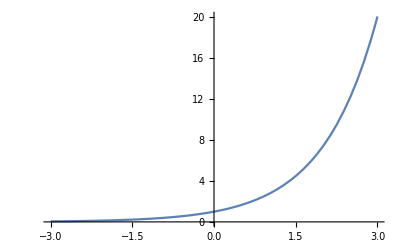

```mathematica
Plot[{A},{x,-3,3}]
```

/. Replace All

### Straight Integration

```mathematica
x =.
```

```mathematica
y =.
```

```mathematica
Clear All
```

All Clear

```mathematica
sol2 = DSolve[y'[x] == x^2, y[x] ,x]
```

{{y[x]→x^3/3+C[1]}}

```mathematica
B1 = y[x]/.sol2/.{C[1] -> 2}
```

{2+x^3/3}

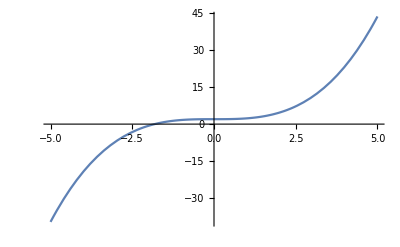

```mathematica
Plot[B1,{x,-5,5}]
```

#### Another Method

```mathematica
B1 = Table[y[x]/. sol2/. {C[1] -> k},{k,2,5}]
```

{{2+x^3/3},{3+x^3/3},{4+x^3/3},{5+x^3/3}}

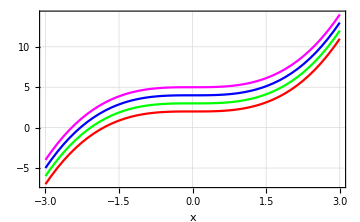

```mathematica
Plot[B1,{x,-3,3},PlotStyle->{Red,Green,Blue,Magenta},GridLines->Automatic,Frame->True , AxesOrigin->{0,0}, AxesLabel->Automatic, ImageSize -> Medium]
```

#### Separable Equations

```mathematica
A = DSolve[y'[x] == 2 x y[x]/(x+1),y[x],x]
```

{{y[x]→ⅇ^(2 (x-Log[1+x])) C[1]}}

```mathematica
B1 = Table[y[x]/.A/.{C[1]-> k},{k,2,5}]
```

{{2 ⅇ^(2 (x-Log[1+x]))},{3 ⅇ^(2 (x-Log[1+x]))},{4 ⅇ^(2 (x-Log[1+x]))},{5 ⅇ^(2 (x-Log[1+x]))}}

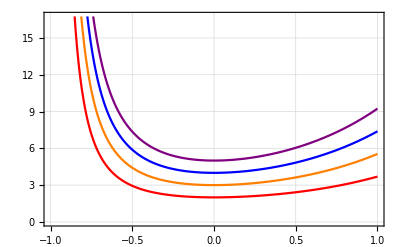

```mathematica
Plot[{B1},{x,-1,1}, PlotStyle->{Red,Orange,Blue, Purple}, GridLines -> Automatic ,Frame -> True,AxesOrigin->{0,0}]
```

```mathematica
sol2 = DSolve[{y'[x] == y[x] +2/ x*y[x],y[1] == 1},y[x],x]
```

{{y[x]→ⅇ^(-1+x) x^2}}

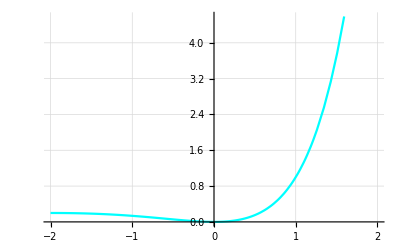

```mathematica
Plot[y[x]/.sol2,{x,-2,2},PlotStyle -> Cyan , GridLines -> Automatic]
```

#### Homogeneous Equation

```mathematica
sol3 = DSolve[y'[x] == (x+y[x])/ x,y[x],x]
```

{{y[x]→x C[1]+x Log[x]}}

```mathematica
sol4 = Table[y[x]/.sol3/.{C[1]->k},{k,2,5}]
```

{{2 x+x Log[x]},{3 x+x Log[x]},{4 x+x Log[x]},{5 x+x Log[x]}}

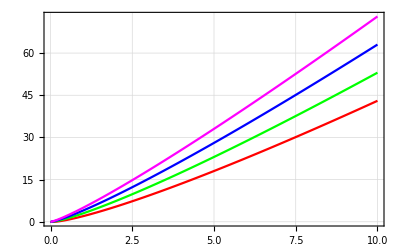

```mathematica
Plot[{sol4}, {x,0,10},PlotStyle -> {Red,Green,Blue,Magenta},GridLines->Automatic,Frame->True , AxesOrigin->{0,0}]
```

#### Linear First order Equations

```mathematica
sol5 = DSolve[y'[x]+y[x]/x == x^2,y[x],x]
```

{{y[x]→x^3/4+C[1]/x}}

```mathematica
sol6 = Table[y[x]/.sol5/.{C[1]->k},{k,2,5}]
```

{{2/x+x^3/4},{3/x+x^3/4},{4/x+x^3/4},{5/x+x^3/4}}

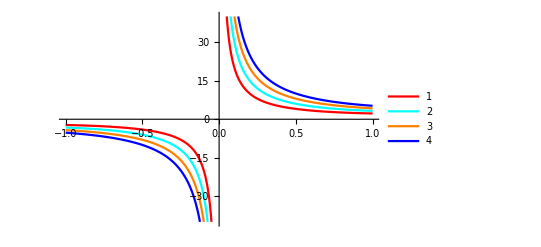

```mathematica
Plot[{sol6},{x,-1,1},PlotStyle-> {Red, Cyan ,Orange ,Blue},PlotLegends->Automatic]
```

```mathematica
Plot[{sol6},{x,-1,1},PlotStyle-> {Red, Cyan ,Orange ,Blue},PlotLegends->Placed[Automatic,Below]]
```

-Graphics-

```mathematica
sol7 = DSolve[{y'[x]*Tan[x]== 2* y[x]-8,y[Pi/2] ==0},y[x],x]
```

{{y[x]→-4 (-1+Sin[x]^2)}}

```mathematica
(*DSolve[{(Tan[x]==-8+2 y[x])==Cot[x] (-8+2 y[x]),y[π/2]==0},y[x],x]*)
```

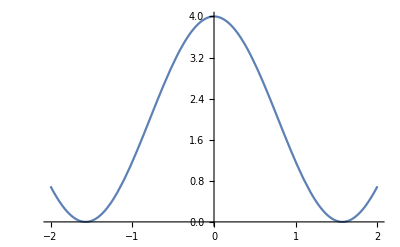

```mathematica
Plot[y[x]/.sol7,{x,-2,2}]
```

```mathematica
Plot[y[x]/.sol7,{x,-5,5}]
```

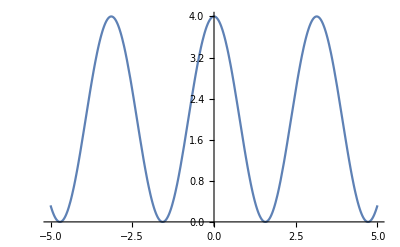

#### Bernoulli Equations

```mathematica
sol8 = DSolve[x*y'[x]+y[x] == y[x]^2x^2+1,y[x],x]
```

{{y[x]→Tan[x+C[1]]/x}}

```mathematica
sol9 = Table[y[x]/. sol8/.{C[1]-> k},{k,1,4}]
```

{{Tan[1+x]/x},{Tan[2+x]/x},{Tan[3+x]/x},{Tan[4+x]/x}}

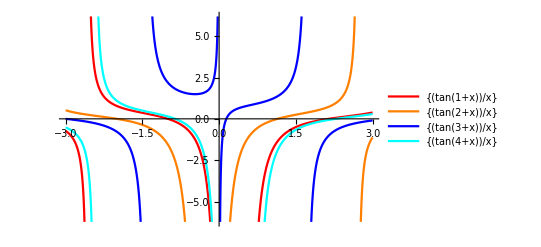

```mathematica
Plot[{sol9},{x,-3,3}, PlotStyle->{Red, Orange, Blue, Cyan},PlotLegends->Placed["Expressions",Right]]
```

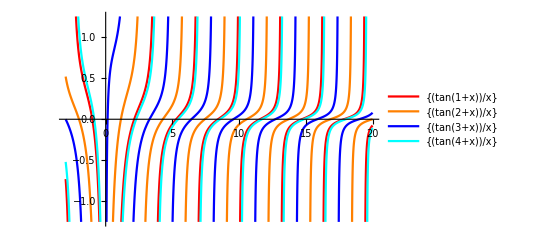

```mathematica
Plot[{sol9},{x,-3,20}, PlotStyle->{Red, Orange, Blue, Cyan},PlotLegends->Placed["Expressions",Right]]
```

#### Exact Equations

```mathematica
M1 [x_, y_] := (x*y^2+2)
N1[x_, y_] := (y*x^2)
Simplify[D[M1[x,y],y] - D[N1[x,y],x]]
```

0